# The “Repressilator”

## Notes for the 2018/19 course “Translational Genomics and Computational Biology”

Marco Antoniotti

Dipartimento di Informatica, Sistemistica e Comunicazione
Università degli Studi di Milano-Bicocca, Milan, Italy
and
Tandon School of Engineering
New York University, New York, USA

Elowitz e Leibler's paper "A synthetic oscillatory network of transcriptional regulators" (Nature, 403, 2000) contains a description of the actual biological, in-vivo, implementation of an oscillatory system initially modeled as a set of differential equations.  The set of ordinary differential equations (ODEs) is listed hereafter. The equations are six and coupled.  Each pair of equations has the following form

(ⅆ m_i)/ⅆt=-m_i+α/(p_j^n+1)+α_0

(ⅆ p_i)/ⅆt=-β(p_i-m_i)

where each m_i represents the amount of mRNA corresponding to each repressor/protein p_i.  The indexes are arranged in a circular manner, with i={lacl,tetR,cl} and j = {cl,lacl,tetR}.
The key elements of this set of six equations are the following. Each equation represents the rate of change over time of either mRNA or repressor/protein.  The equation representing the change over time of mRNA depends on the amount of mRNA present and on the amount of repressor/protein present.  When the amount of repressor/protein present is low, then its rate of change depends essentially on the parameters α and α_0, which should be chosen appropriately.  When the amount of repressor/protein is high, then the rate of change of the "controlled" mRNA is essentially α_0-m_i. The equation representing the change of repressor/protein represent a positive changein the presence of a lot of mRNA "coding" for the repressor/protein, and a negative change when the amount of mRNA is "low" (and the corresponding amount of protein is "high").
As repressor/protein and controlled mRNA go up and down the "reporter" protein GFP tied to terR (cfr., the paper) goes up and down too.

Note that the mathematical model is relatively simple and it makes a slew of assumptions (which may or may not be warranted, as the experiments show).  The parameters α, α_0, n, and β are the same for each equation, this has the advantage of making the system easy to explain and to "run".  As a model of "reality" it will need a lot of fine tuning and diversification of all the relevant parameters involved.

In the following, there is an actual implementation of the simple repressilator set of six ODEs in Mathematica.

## The equations

The following equations in Mathematica represent the simple repressilator system.  The nomenclature of the variables (i.e., of the functions of time t) is the following.  Each mRNA is named by a lowercase identifier, while each repressor/protein is represented by a capitalized identifier.  That is m_lacl becomes lacl[t], and becomes p_tetR becomes TetR[t].  Derivatives are noted with the usual '.

Each equation is saved in a variable named eqnK.

```mathematica
eqn1 = lacl'[t] == -lacl[t] + (alpha /(1+ Cl[t]^n)) + alpha0
```

lacl'[t]==alpha0+alpha/(1+Cl[t]^n)-lacl[t]

```mathematica
eqn2 = Lacl'[t] == -beta(Lacl[t] - lacl[t])
```

Lacl'[t]==-beta (-lacl[t]+Lacl[t])

```mathematica
eqn3 =tetR'[t] == -tetR [t]+ (alpha / (1 + Lacl[t]^n)) +alpha0
```

tetR'[t]==alpha0+alpha/(1+Lacl[t]^n)-tetR[t]

```mathematica
eqn4 = TetR'[t] == -beta(TetR[t] - tetR[t])
```

TetR'[t]==-beta (-tetR[t]+TetR[t])

```mathematica
eqn5 = cl'[t] == -cl[t] +(alpha/(1+TetR[t]^n)) +alpha0
```

cl'[t]==alpha0-cl[t]+alpha/(1+TetR[t]^n)

```mathematica
eqn6 = Cl'[t] == -beta(Cl[t] - cl[t])
```

Cl'[t]==-beta (-cl[t]+Cl[t])

### Parameters

The parameters are the following and they are taken from various sources.  The interplay among them yields very striking results when numerically integrating the set of ODEs.

```mathematica
n = 5
```

5

```mathematica
alpha = 220
```

220

```mathematica
beta=2
```

2

```mathematica
alpha0=5.0 10^-4
```

0.0005

### Initial conditions

The initial mRNA conditions should not all be the same, otherwise the system will not exhibit the oscillations.

```mathematica
i1 =lacl[0] == 10
```

lacl[0]==10

```mathematica
i2 = Lacl[0]==1
```

Lacl[0]==1

```mathematica
i3 = tetR[0]==1
```

tetR[0]==1

```mathematica
i4= TetR[0]==1
```

TetR[0]==1

```mathematica
i5=cl[0]== 1
```

cl[0]==1

```mathematica
i6= Cl[0]==1
```

Cl[0]==1

### Solution (i.e., simulation)

To run or simulate the Repressilator model we just solve (numerically) the set of equations.  The command to do so is the following.  The result is strange-looking, but it is what we expect.

```mathematica
eqngraphs =NDSolve[{eqn1, eqn2, eqn3, eqn4, eqn5, eqn6,i1, i2, i3, i4, i5, i6},{Lacl, TetR, Cl,lacl, tetR, cl},{t,0,500}]
```

{{Lacl→InterpolatingFunction[…],TetR→InterpolatingFunction[…],Cl→InterpolatingFunction[…],lacl→InterpolatingFunction[…],tetR→InterpolatingFunction[…],cl→InterpolatingFunction[…]}}

Now we can plot the results.  The following command plots the amounts of repressor/protein against time.  The plot changes dramatically when the set of values of the parameters are modified.

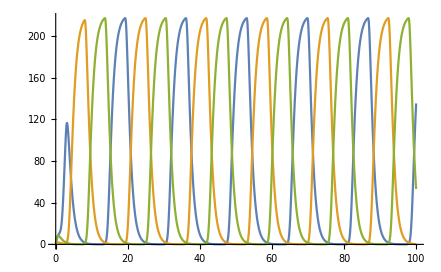

```mathematica
Plot[Evaluate[{Cl[t],TetR[t],Lacl[t]}/.eqngraphs],{t,0,100},PlotRange-> All,AxesOrigin->{0,0}]
```

The following command plots the amounts of mRNAs against time.

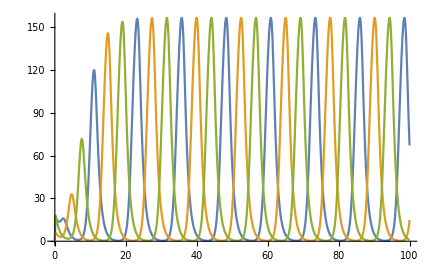

```mathematica
Plot[Evaluate[{cl[t],tetR[t],lacl[t]}/.eqngraphs],{t,0,100},PlotRange-> All,AxesOrigin->{0,0}]
```

The following command plots the amounts of mRNAs versus the associated repressor/protein (tetR and TetR) agains time.  As you can see there is a delay in the plots, which "represents" the translation time.

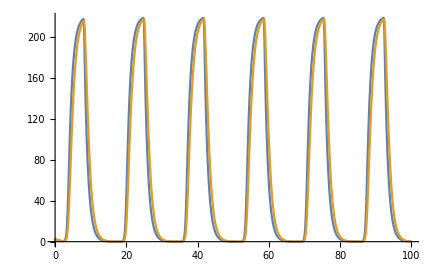

```mathematica
Plot[Evaluate[{tetR[t],TetR[t]}/.eqngraphs],{t,0,100},PlotRange-> All,AxesOrigin->{0,0}]
```